```mathematica
OutPutPath="ParralelD10";
SetDirectory[NotebookDirectory[]];
$P=2^31-1;
diffInvariants={mt2,s12,s123,s23,s234,s34,s345,s45,s56};
For[i=1,i<=9,i++,			
dhxbMatrices[diffInvariants[[i]]]=ReadList[FileNameJoin[{Directory[],ToString[StringForm["``/DEmatrix_d``",OutPutPath,diffInvariants[[i]]]]}]];
]
phasespacepoints=ReadList[FileNameJoin[{Directory[],ToString[StringForm["``/parameters",OutPutPath]]}]];
RationalReconstruct[a_]:=With[{v=LatticeReduce[{{a,1},{$P,0}}][[1]]},v[[1]]/v[[2]]];
```

```mathematica
powerReconstruct[pars_,FitVecIn_]:=Module[{pars2,AnsatzPowersNumi,FitVec,AnsatzPowersDeno,MatNumiPart,onevc,parsCutOne,reconstructedFit,AnsatzPowersDenoOne,
fit,solrule,MatDenoPart,Solset,FinalMat,sol3,Ansatz,MaxPower},
	MaxPower=9;
AnsatzPowersNumi=FrobeniusSolve[{1,1},MaxPower];
	AnsatzPowersDeno=FrobeniusSolve[{1,1},MaxPower];
	pars2=pars/.{x_Integer:>{x,1}};
	(*MatNumiPart=Parallelize@Outer[m31ExpDot,pars2,AnsatzPowersNumi,1];*)

	MatNumiPart=Table[Table[Times@@PowerMod[pars2[[i]],AnsatzPowersNumi[[q]],$P],{q,1,Length[AnsatzPowersNumi]}],{i,1,Length[pars2]}];
	(*Table[Times@@PowerMod[pars2[[1]],AnsatzPowersNumi[[q]],$P],{q,1,Length[AnsatzPowersNumi]}]//Echo;*)
	
	FitVec=Expand[-FitVecIn,Modulus->$P];
	onevc=Table[{1},MaxPower+1];
	parsCutOne=MapThread[Join,{pars2,Transpose[{FitVec}]}];
	AnsatzPowersDenoOne=MapThread[Join,{AnsatzPowersDeno,onevc}];

	(*MatDenoPart=Parallelize@Outer[m31ExpDot,parsCutOne,AnsatzPowersDenoOne,1];*)
	
	MatDenoPart=Table[Table[Times@@PowerMod[parsCutOne[[i]],AnsatzPowersDenoOne[[j]],$P],{j,1,Length[AnsatzPowersDenoOne]}],{i,1,Length[parsCutOne]}];
	
	FinalMat=Expand[MapThread[Join,{MatNumiPart,MatDenoPart}],Modulus->$P];

	
	sol3=NullSpace[FinalMat,Modulus->$P];
	Ansatz=Sum[fac[n]t^n,{n,0,MaxPower}]/Sum[fac[n+MaxPower+1]t^n,{n,0,MaxPower}];
	Solset=Cases[Ansatz,fac[___],Infinity];
	solrule=Thread[Rule[Solset,sol3[[1]]]];
	fit=Together[Ansatz/.solrule]//ExpandDenominator//ExpandNumerator;
	Return[Expand[fit,Modulus->$P]]
]
```

```mathematica
LaunchKernels[20];
```

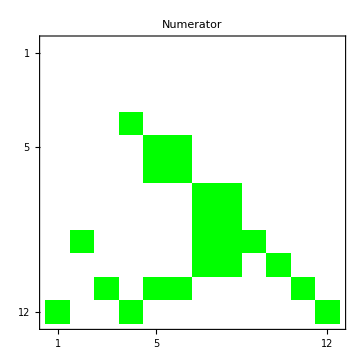
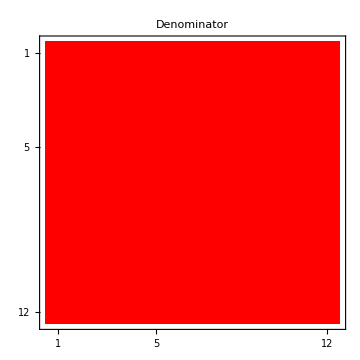
-Graphics- | -Graphics- |

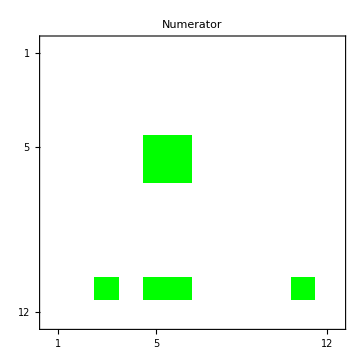
-Graphics- | -Graphics- |

-Graphics- | -Graphics- |

-Graphics- | -Graphics- |

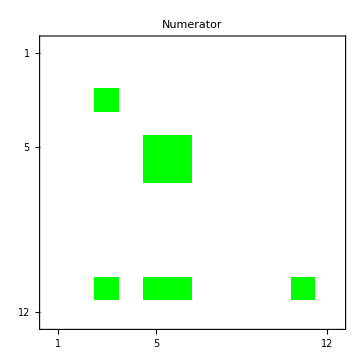
-Graphics- | -Graphics- |

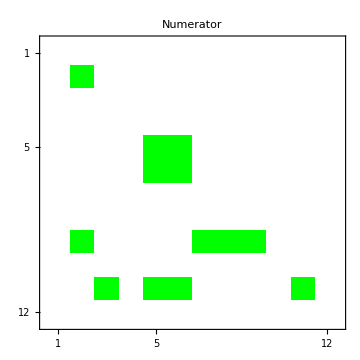
-Graphics- | -Graphics- |

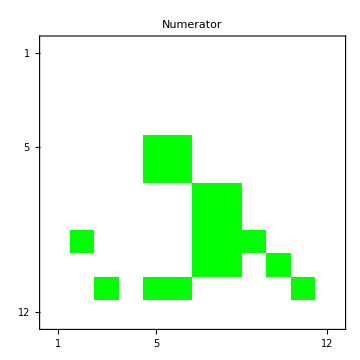
-Graphics- | -Graphics- |

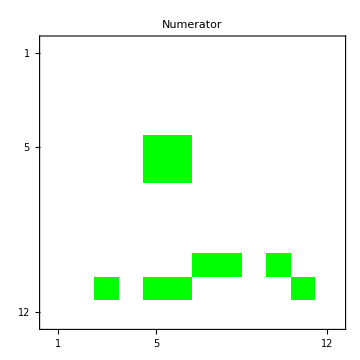
-Graphics- | -Graphics- |

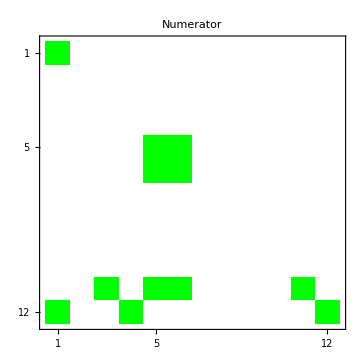
-Graphics- | -Graphics- |

```mathematica
colors={-1->White,0->Red,1->Green,2->Blue,3->Yellow,4->Orange,5->RGBColor["#e09f7d"],6->RGBColor["#EF5D60"],7->RGBColor["#EC4067"],8->RGBColor["#A01A7D"],9->RGBColor["#703399"],10->RGBColor["#0B050F"]};
CutsA=1;
CutsB=12;
For[i=1,i<=9,i++,
MatReco[diffInvariants[[i]]]=ParallelTable[Quiet[Expand[powerReconstruct[phasespacepoints[[All,1]],dhxbMatrices[diffInvariants[[i]]][[All,pos]]]/.{t->4-2ϵ},Modulus->$P]],{pos,1,12^2}];
NumiPowers=Exponent[Numerator[MatReco[diffInvariants[[i]]]],ϵ]/.{-Infinity->-1};
DenoPowers=Exponent[Denominator[MatReco[diffInvariants[[i]]]],ϵ];
NumiPowersMat=NumiPowers//Normal;
DenoPowersMat=DenoPowers//Normal;
(*NonZerosPos=ReadList[FileNameJoin[{NotebookDirectory[],"files/NonZeroList.txt"}]];
NumiPowersMat=ConstantArray[-1,241^2];
NumiPowersMat[[NonZerosPos]]=NumiPowers;
DenoPowersMat=ConstantArray[-1,241^2];
DenoPowersMat[[NonZerosPos]]=DenoPowers;*)
P1=MatrixPlot[ArrayReshape[NumiPowersMat,{12,12}][[CutsA;;CutsB,CutsA;;CutsB]],ColorRules->colors,PlotLabel->"Numerator",ImageSize->Medium];
P2=MatrixPlot[ArrayReshape[DenoPowersMat,{12,12}][[CutsA;;CutsB,CutsA;;CutsB]],ColorRules->colors,PlotLabel->"Denominator",ImageSize->Medium];
L1=SwatchLegend[Values@colors[[2;;]],Keys@colors[[2;;]],LegendFunction->"Frame",LegendLayout->"Column",LegendLabel->diffInvariants[[i]]];
Print[Grid[{{P1,P2,L1}}]];
]
```

```mathematica
ArrayReshape[MatReco[diffInvariants[[5]]],{12,12}]
```

```mathematica
Expand[Sum[RandomInteger[2^31-1]*ArrayReshape[MatReco[diffInvariants[[ii]]],{12,12}],{ii,1,9}], Modulus->2^31-1]//MatrixForm
```

(1669416687 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 1656139275 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 1328388445 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 1053899357 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1284972265 ϵ | 504191312 ϵ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 1353910414 ϵ | 45516733 ϵ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1551401694 ϵ | 1270925662 ϵ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1516222592 ϵ | 659531680 ϵ | 0 | 0 | 0 | 0
0 | 1104732252 ϵ | 0 | 0 | 0 | 0 | 494216132 ϵ | 1595117521 ϵ | 1609232286 ϵ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 83059689 ϵ | 895153144 ϵ | 0 | 430516814 ϵ | 0 | 0
0 | 0 | 1712001 ϵ | 0 | 177268089 ϵ | 1072885823 ϵ | 0 | 0 | 0 | 0 | 685275942 ϵ | 0
398474956 ϵ | 0 | 0 | 199237478 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 734883904 ϵ)

```mathematica
ArrayReshape[MatReco[diffInvariants[[5]]],{12,12}]//MatrixForm
ArrayReshape[MatReco[diffInvariants[[7]]],{12,12}]//MatrixForm
```

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 368326278 ϵ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 127702839 ϵ | 808167246 ϵ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 551486954 ϵ | 531149155 ϵ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 2080755808 ϵ | 0 | 2069928970 ϵ | 1107105743 ϵ | 0 | 0 | 0 | 0 | 2041383376 ϵ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

(0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 918316041 ϵ | 511856723 ϵ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 721759885 ϵ | 1123770201 ϵ | 0 | 0 | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 175265885 ϵ | 997174281 ϵ | 0 | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 1752690277 ϵ | 153135085 ϵ | 0 | 0 | 0 | 0
0 | 1231977709 ϵ | 0 | 0 | 0 | 0 | 1288881437 ϵ | 457752969 ϵ | 311474692 ϵ | 0 | 0 | 0
0 | 0 | 0 | 0 | 0 | 0 | 197396685 ϵ | 997174281 ϵ | 0 | 1032343794 ϵ | 0 | 0
0 | 0 | 537877367 ϵ | 0 | 1132007677 ϵ | 804803140 ϵ | 0 | 0 | 0 | 0 | 1261321630 ϵ | 0
0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0 | 0)

$Failed